```mathematica
L = 5
```

5

```mathematica
T = 240
```

240

```mathematica
U = 1
```

1

```mathematica
(* CP is 1/2 of base LP pool liquidity in millions of dollars *)
```

```mathematica
CP = 10
```

10

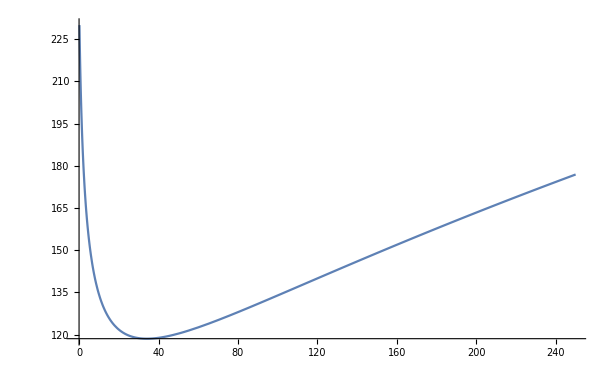

```mathematica
Plot[Piecewise[{{CP*(T/(L*Abs[x]) + U)*(1/Sqrt[1-Abs[x]] - 1),x<0},{CP*(T/(L*x) + U)*(Sqrt[1+x]-1),x>0}}],{x,-1,250}]
```

```mathematica
FindMinimum[CP*(T/(L*x) + U)*(Sqrt[1+x]-1),x]
```

{118.564,{x→34.1436}}

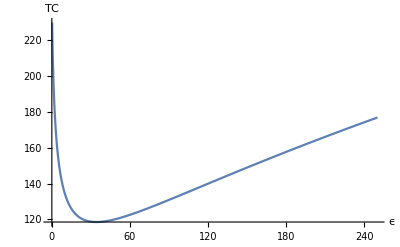

```mathematica
Show[%27,AxesLabel->{HoldForm[ϵ],HoldForm[TC]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/Users/personal/Desktop/tc_10m.svg",%30,"SVG"]
```

/Users/personal/Desktop/tc_10m.svg

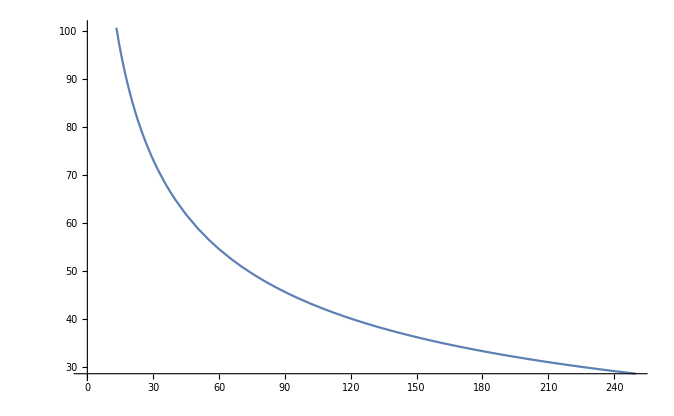

```mathematica
Plot[Piecewise[{{CP*(T/(L*Abs[x]))*(1/Sqrt[1-Abs[x]] - 1),x<0},{CP*(T/(L*x))*(Sqrt[1+x]-1),x>0}}],{x,-1,250}]
```

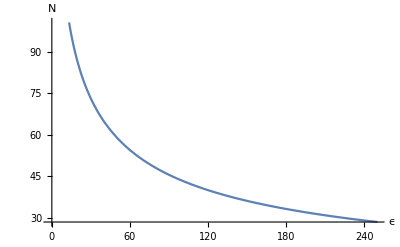

```mathematica
Show[%36,AxesLabel->{HoldForm[ϵ],HoldForm[N]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
CP*(T/(L*34.14359353944894))*(Sqrt[1+34.14359353944894]-1)
```

69.282

```mathematica
(* Caps on OI can be made s.t. N break-even in [35] is not possible *)
```